```mathematica
{{{n}, {n}}}//InputForm
```

```mathematica
TraditionalForm[{{{n}, {n}}}]
```

({n} | {n})

```mathematica
{{{n},{n}}}
```

```mathematica
{{{n}, {k}}}
```

```mathematica
Style[StirlingS2["10",20],40]
```

{10
20}

```mathematica
LatexForm[StirlingS2[n,k]]
```

LatexForm[StirlingS2[n,k]]

```mathematica
MakeBoxes[StirlingS2[n_,k_],StandardForm]:=RowBox[{"{",GridBox[{{n},{k}},AutoDelete->False,GridBoxItemSize->{"Columns"->{{Automatic}},"Rows"->{{Automatic}}}],"}"}]
```

```mathematica
MakeBoxes[StirlingS1[n_,k_],StandardForm]:=RowBox[{"[",GridBox[{{n},{k}},AutoDelete->False,GridBoxItemSize->{"Columns"->{{Automatic}},"Rows"->{{Automatic}}}],"]"}]
```

```mathematica
TableForm[Table[{n,3n-6},,{n,1,20}]]
```

1 | -3
2 | 0
3 | 3
4 | 6
5 | 9
6 | 12
7 | 15
8 | 18
9 | 21
10 | 24
11 | 27
12 | 30
13 | 33
14 | 36
15 | 39
16 | 42
17 | 45
18 | 48
19 | 51
20 | 54

```mathematica
maxmin5=Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},ChromaticPolynomial[g,4]==24&&VertexCount[g]==5&& PlanarGraphQ[g]]&]
```

{29523,29521,29515,29497,29443,29281,28795,27337,22963,9841}

```mathematica
Table[Labeled[Graph[EdgeList[allGraphs5[k,"graph"]],GraphLayout->"PlanarEmbedding",ImageSize->100],k],{k,maxmin5}]
```

{-Graphics-29523,-Graphics-29521,-Graphics-29515,-Graphics-29497,-Graphics-29443,-Graphics-29281,-Graphics-28795,-Graphics-27337,-Graphics-22963,-Graphics-9841}

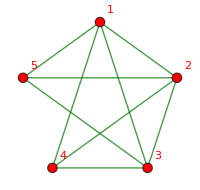
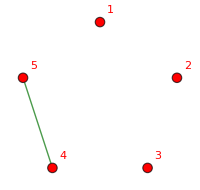
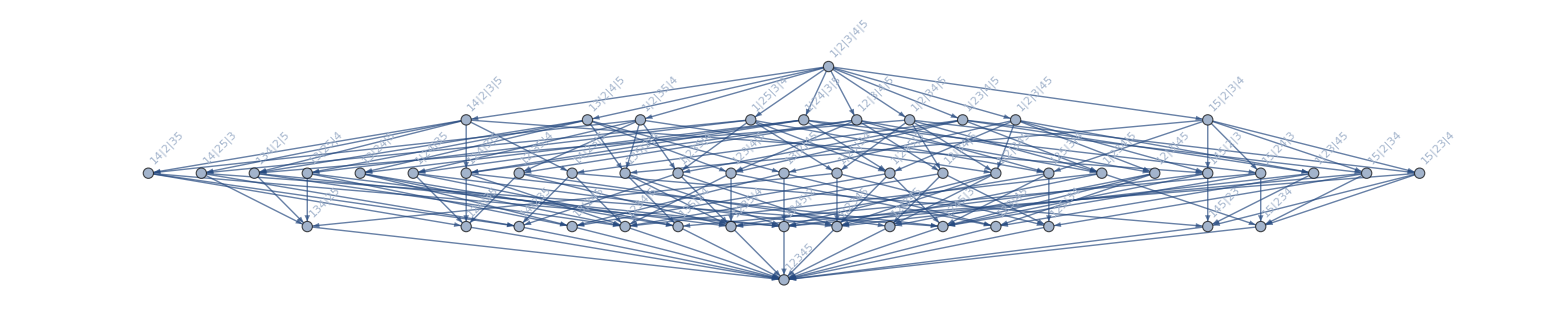
-Graphics-29523 | -Graphics-1
-Graphics-
-Graphics-18 n12345-6 n1234x5-6 n1235x4+2 n123x4x5-4 n1245x3-2 n124x35+2 n124x3x5-2 n125x34+2 n125x3x4-n12x345+n12x34x5+n12x35x4-n12x3x4x5-4 n1345x2-2 n134x25+2 n134x2x5-2 n135x24+2 n135x2x4-n13x245+n13x24x5+n13x25x4-n13x2x4x5-n145x23+n145x2x3-2 n14x235+n14x23x5+n14x25x3+n14x2x35-n14x2x3x5-2 n15x234+n15x23x4+n15x24x3+n15x2x34-n15x2x3x4-4 n1x2345+2 n1x234x5+2 n1x235x4-n1x23x4x5+n1x245x3+n1x24x35-n1x24x3x5+n1x25x34-n1x25x3x4+n1x2x345-n1x2x34x5-n1x2x35x4+n1x2x3x4x5x^5-9 x^4+29 x^3-39 x^2+18 x
(x-3)^2 (x-2) (x-1) x
 *  * 00024240
-Graphics-+-Graphics-

```mathematica
SummaryPrintGood5[29523]
```

```mathematica
maxmin=Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},ChromaticPolynomial[g,4]==24&&VertexCount[g]==6&& PlanarGraphQ[g]]&]
```

{7174416,7174414,7174368,7174360,7174342,7174336,7174206,7174200,7174182,7174174,7174128,7174126,7173714,7173712,7173642,7173616,7173478,7173454,7172262,7172254,7172238,7172158,7172014,7171942,7171534,7171528,7171510,7171456,7167888,7167882,7167862,7167802,7167622,7167568,7167162,7167154,7167136,7166920,7165704,7165702,7165624,7165462,7154742,7154740,7154688,7154680,7154524,7154518,7154040,7154038,7153960,7153798,7152582,7152574,7152556,7152340,7148206,7148200,7148182,7148128,7115394,7115392,7115322,7115296,7115158,7115134,7113216,7112488,7108840,7108114,7095694,7094992,6997302,6997294,6997278,6997198,6997054,6996982,6996576,6994390,6990736,6988558,6977542,6975436,6938254,6938248,6938230,6938176,6937528,6936070,6643008,6643002,6642982,6642922,6642742,6642688,6642280,6640816,6635722,6634264,6623086,6616768,6583962,6583954,6583936,6583720,6583234,6577402,6465864,6465862,6465784,6465622,6463678,6459304,5580102,5580100,5580048,5580040,5579884,5579878,5579374,5577862,5573326,5559718,5558260,5553886,5521080,5521078,5521000,5520838,5520352,5501398,5402982,5402974,5402956,5402740,5400796,5383300,5048686,5048680,5048662,5048608,5042128,5029006,2390754,2390752,2390728,2389296,2389288,2389216,2384920,2384914,2384680,2371774,2371720,2371558,2332434,2332432,2332408,2330248,2325874,2312752,2214336,2214328,2214256,2213608,2207776,2194654,1860040,1860034,1859800,1859314,1857856,1840360,797134,797080,796918,796432,794974,790600}

```mathematica
Table[Labeled[Graph[EdgeList[allGraphs6[k,"graph"]],GraphLayout->"PlanarEmbedding",ImageSize->100],k],{k,maxmin}]
```

{-Graphics-7174416,-Graphics-7174414,-Graphics-7174368,-Graphics-7174360,-Graphics-7174342,-Graphics-7174336,-Graphics-7174206,-Graphics-7174200,-Graphics-7174182,-Graphics-7174174,-Graphics-7174128,-Graphics-7174126,-Graphics-7173714,-Graphics-7173712,-Graphics-7173642,-Graphics-7173616,-Graphics-7173478,-Graphics-7173454,-Graphics-7172262,-Graphics-7172254,-Graphics-7172238,-Graphics-7172158,-Graphics-7172014,-Graphics-7171942,-Graphics-7171534,-Graphics-7171528,-Graphics-7171510,-Graphics-7171456,-Graphics-7167888,-Graphics-7167882,-Graphics-7167862,-Graphics-7167802,-Graphics-7167622,-Graphics-7167568,-Graphics-7167162,-Graphics-7167154,-Graphics-7167136,-Graphics-7166920,-Graphics-7165704,-Graphics-7165702,-Graphics-7165624,-Graphics-7165462,-Graphics-7154742,-Graphics-7154740,-Graphics-7154688,-Graphics-7154680,-Graphics-7154524,-Graphics-7154518,-Graphics-7154040,-Graphics-7154038,-Graphics-7153960,-Graphics-7153798,-Graphics-7152582,-Graphics-7152574,-Graphics-7152556,-Graphics-7152340,-Graphics-7148206,-Graphics-7148200,-Graphics-7148182,-Graphics-7148128,-Graphics-7115394,-Graphics-7115392,-Graphics-7115322,-Graphics-7115296,-Graphics-7115158,-Graphics-7115134,-Graphics-7113216,-Graphics-7112488,-Graphics-7108840,-Graphics-7108114,-Graphics-7095694,-Graphics-7094992,-Graphics-6997302,-Graphics-6997294,-Graphics-6997278,-Graphics-6997198,-Graphics-6997054,-Graphics-6996982,-Graphics-6996576,-Graphics-6994390,-Graphics-6990736,-Graphics-6988558,-Graphics-6977542,-Graphics-6975436,-Graphics-6938254,-Graphics-6938248,-Graphics-6938230,-Graphics-6938176,-Graphics-6937528,-Graphics-6936070,-Graphics-6643008,-Graphics-6643002,-Graphics-6642982,-Graphics-6642922,-Graphics-6642742,-Graphics-6642688,-Graphics-6642280,-Graphics-6640816,-Graphics-6635722,-Graphics-6634264,-Graphics-6623086,-Graphics-6616768,-Graphics-6583962,-Graphics-6583954,-Graphics-6583936,-Graphics-6583720,-Graphics-6583234,-Graphics-6577402,-Graphics-6465864,-Graphics-6465862,-Graphics-6465784,-Graphics-6465622,-Graphics-6463678,-Graphics-6459304,-Graphics-5580102,-Graphics-5580100,-Graphics-5580048,-Graphics-5580040,-Graphics-5579884,-Graphics-5579878,-Graphics-5579374,-Graphics-5577862,-Graphics-5573326,-Graphics-5559718,-Graphics-5558260,-Graphics-5553886,-Graphics-5521080,-Graphics-5521078,-Graphics-5521000,-Graphics-5520838,-Graphics-5520352,-Graphics-5501398,-Graphics-5402982,-Graphics-5402974,-Graphics-5402956,-Graphics-5402740,-Graphics-5400796,-Graphics-5383300,-Graphics-5048686,-Graphics-5048680,-Graphics-5048662,-Graphics-5048608,-Graphics-5042128,-Graphics-5029006,-Graphics-2390754,-Graphics-2390752,-Graphics-2390728,-Graphics-2389296,-Graphics-2389288,-Graphics-2389216,-Graphics-2384920,-Graphics-2384914,-Graphics-2384680,-Graphics-2371774,-Graphics-2371720,-Graphics-2371558,-Graphics-2332434,-Graphics-2332432,-Graphics-2332408,-Graphics-2330248,-Graphics-2325874,-Graphics-2312752,-Graphics-2214336,-Graphics-2214328,-Graphics-2214256,-Graphics-2213608,-Graphics-2207776,-Graphics-2194654,-Graphics-1860040,-Graphics-1860034,-Graphics-1859800,-Graphics-1859314,-Graphics-1857856,-Graphics-1840360,-Graphics-797134,-Graphics-797080,-Graphics-796918,-Graphics-796432,-Graphics-794974,-Graphics-790600}

```mathematica
rep6=Table[allGraphs6[k,"colofour"]->allGraphs6[k,"graph"],{k,allGraphs6AtomKeys}]
```

{v1x2x3x4x5x6→-Graphics-,v1x2x3x4x56→-Graphics-,v1x2x3x46x5→-Graphics-,v1x2x3x45x6→-Graphics-,v1x2x3x456→-Graphics-,v1x2x36x4x5→-Graphics-,v1x2x36x45→-Graphics-,v1x2x35x4x6→-Graphics-,v1x2x35x46→-Graphics-,v1x2x356x4→-Graphics-,v1x2x34x5x6→-Graphics-,v1x2x34x56→-Graphics-,v1x2x346x5→-Graphics-,v1x2x345x6→-Graphics-,v1x2x3456→-Graphics-,v1x26x3x4x5→-Graphics-,v1x26x3x45→-Graphics-,v1x26x35x4→-Graphics-,v1x26x34x5→-Graphics-,v1x26x345→-Graphics-,v1x25x3x4x6→-Graphics-,v1x25x3x46→-Graphics-,v1x25x36x4→-Graphics-,v1x25x34x6→-Graphics-,v1x25x346→-Graphics-,v1x256x3x4→-Graphics-,v1x256x34→-Graphics-,v1x24x3x5x6→-Graphics-,v1x24x3x56→-Graphics-,v1x24x36x5→-Graphics-,v1x24x35x6→-Graphics-,v1x24x356→-Graphics-,v1x246x3x5→-Graphics-,v1x246x35→-Graphics-,v1x245x3x6→-Graphics-,v1x245x36→-Graphics-,v1x2456x3→-Graphics-,v1x23x4x5x6→-Graphics-,v1x23x4x56→-Graphics-,v1x23x46x5→-Graphics-,v1x23x45x6→-Graphics-,v1x23x456→-Graphics-,v1x236x4x5→-Graphics-,v1x236x45→-Graphics-,v1x235x4x6→-Graphics-,v1x235x46→-Graphics-,v1x2356x4→-Graphics-,v1x234x5x6→-Graphics-,v1x234x56→-Graphics-,v1x2346x5→-Graphics-,v1x2345x6→-Graphics-,v1x23456→-Graphics-,v16x2x3x4x5→-Graphics-,v16x2x3x45→-Graphics-,v16x2x35x4→-Graphics-,v16x2x34x5→-Graphics-,v16x2x345→-Graphics-,v16x25x3x4→-Graphics-,v16x25x34→-Graphics-,v16x24x3x5→-Graphics-,v16x24x35→-Graphics-,v16x245x3→-Graphics-,v16x23x4x5→-Graphics-,v16x23x45→-Graphics-,v16x235x4→-Graphics-,v16x234x5→-Graphics-,v16x2345→-Graphics-,v15x2x3x4x6→-Graphics-,v15x2x3x46→-Graphics-,v15x2x36x4→-Graphics-,v15x2x34x6→-Graphics-,v15x2x346→-Graphics-,v15x26x3x4→-Graphics-,v15x26x34→-Graphics-,v15x24x3x6→-Graphics-,v15x24x36→-Graphics-,v15x246x3→-Graphics-,v15x23x4x6→-Graphics-,v15x23x46→-Graphics-,v15x236x4→-Graphics-,v15x234x6→-Graphics-,v15x2346→-Graphics-,v156x2x3x4→-Graphics-,v156x2x34→-Graphics-,v156x24x3→-Graphics-,v156x23x4→-Graphics-,v156x234→-Graphics-,v14x2x3x5x6→-Graphics-,v14x2x3x56→-Graphics-,v14x2x36x5→-Graphics-,v14x2x35x6→-Graphics-,v14x2x356→-Graphics-,v14x26x3x5→-Graphics-,v14x26x35→-Graphics-,v14x25x3x6→-Graphics-,v14x25x36→-Graphics-,v14x256x3→-Graphics-,v14x23x5x6→-Graphics-,v14x23x56→-Graphics-,v14x236x5→-Graphics-,v14x235x6→-Graphics-,v14x2356→-Graphics-,v146x2x3x5→-Graphics-,v146x2x35→-Graphics-,v146x25x3→-Graphics-,v146x23x5→-Graphics-,v146x235→-Graphics-,v145x2x3x6→-Graphics-,v145x2x36→-Graphics-,v145x26x3→-Graphics-,v145x23x6→-Graphics-,v145x236→-Graphics-,v1456x2x3→-Graphics-,v1456x23→-Graphics-,v13x2x4x5x6→-Graphics-,v13x2x4x56→-Graphics-,v13x2x46x5→-Graphics-,v13x2x45x6→-Graphics-,v13x2x456→-Graphics-,v13x26x4x5→-Graphics-,v13x26x45→-Graphics-,v13x25x4x6→-Graphics-,v13x25x46→-Graphics-,v13x256x4→-Graphics-,v13x24x5x6→-Graphics-,v13x24x56→-Graphics-,v13x246x5→-Graphics-,v13x245x6→-Graphics-,v13x2456→-Graphics-,v136x2x4x5→-Graphics-,v136x2x45→-Graphics-,v136x25x4→-Graphics-,v136x24x5→-Graphics-,v136x245→-Graphics-,v135x2x4x6→-Graphics-,v135x2x46→-Graphics-,v135x26x4→-Graphics-,v135x24x6→-Graphics-,v135x246→-Graphics-,v1356x2x4→-Graphics-,v1356x24→-Graphics-,v134x2x5x6→-Graphics-,v134x2x56→-Graphics-,v134x26x5→-Graphics-,v134x25x6→-Graphics-,v134x256→-Graphics-,v1346x2x5→-Graphics-,v1346x25→-Graphics-,v1345x2x6→-Graphics-,v1345x26→-Graphics-,v13456x2→-Graphics-,v12x3x4x5x6→-Graphics-,v12x3x4x56→-Graphics-,v12x3x46x5→-Graphics-,v12x3x45x6→-Graphics-,v12x3x456→-Graphics-,v12x36x4x5→-Graphics-,v12x36x45→-Graphics-,v12x35x4x6→-Graphics-,v12x35x46→-Graphics-,v12x356x4→-Graphics-,v12x34x5x6→-Graphics-,v12x34x56→-Graphics-,v12x346x5→-Graphics-,v12x345x6→-Graphics-,v12x3456→-Graphics-,v126x3x4x5→-Graphics-,v126x3x45→-Graphics-,v126x35x4→-Graphics-,v126x34x5→-Graphics-,v126x345→-Graphics-,v125x3x4x6→-Graphics-,v125x3x46→-Graphics-,v125x36x4→-Graphics-,v125x34x6→-Graphics-,v125x346→-Graphics-,v1256x3x4→-Graphics-,v1256x34→-Graphics-,v124x3x5x6→-Graphics-,v124x3x56→-Graphics-,v124x36x5→-Graphics-,v124x35x6→-Graphics-,v124x356→-Graphics-,v1246x3x5→-Graphics-,v1246x35→-Graphics-,v1245x3x6→-Graphics-,v1245x36→-Graphics-,v12456x3→-Graphics-,v123x4x5x6→-Graphics-,v123x4x56→-Graphics-,v123x46x5→-Graphics-,v123x45x6→-Graphics-,v123x456→-Graphics-,v1236x4x5→-Graphics-,v1236x45→-Graphics-,v1235x4x6→-Graphics-,v1235x46→-Graphics-,v12356x4→-Graphics-,v1234x5x6→-Graphics-,v1234x56→-Graphics-,v12346x5→-Graphics-,v12345x6→-Graphics-,v123456→-Graphics-}

```mathematica
SummaryPrintGood6[k_]:=Block[
{g=MobiusGraphDoubleGood[K6Key,k,allGraphs6], gr=allGraphs6[k,"graph"],compKey=FindComplement[k,allGraphs6],comp={},g2},
comp=allGraphs6[compKey,"graph"];
g2=MobiusGraphDoubleGood[K6Key,compKey,allGraphs6];
Framed[
Labeled[
Column[{
TableForm[{Labeled[Graph[gr,ImageSize->200],Style[k,Bold,12, Underlined,Red]],Labeled[Graph[comp,ImageSize->200],Style[compKey,Bold,12, Underlined,Red]]}, TableDirections->Row],
Graph[g,ImageSize->1800],
Graph[g2,ImageSize->1800]
},Alignment->Center],
{Style[StandardForm[allGraphs6[k,"colofourrealnull"]],Darker[Green],12],
Column[
{Style[TraditionalForm[ ChromaticPolynomial[gr,x]],Blue],Style[TraditionalForm[ ChromaticPolynomial[gr,x]//Factor],Red],Row[Table[Style[ChromaticPolynomial[gr,m],Blue],{m,1,6}], " * "],
Framed[Style[StandardForm[((allGraphs6[k,"colofour"]/.rep6))],Darker[Green],12]]},
Center
]
},
{Top,Bottom,Bottom}
]
]
]
```

```mathematica
SummaryPrintGood6[2330248]
```

$Aborted

```mathematica
FormulaGraph2[formula_]:=Block[{sets=Sort[Map[SymbolToSets[#]&,ListofVars[formula]]], edges={},vertices,pos=1},
Monitor[
Table[
Table[
If[IsRefinement[s1,s2]&&(Length[s1]==Length[s2]-1), AppendTo[edges,SetsToSymbol2[s2]->SetsToSymbol2[s1]]]
,{s2,Select[sets,#≠s1&]}
];pos++
,{s1,sets}],
{Length[edges],pos, Length[sets],s1,s2}
];
vertices = Table[SetsToSymbol[s,"n"]-> SymbolToLabel[ SetsToSymbol2[s]],{s,sets}];
Graph[edges,VertexLabels->vertices, GraphLayout->"LayeredDigraphEmbedding", ImageSize->{200,200}]
]
```

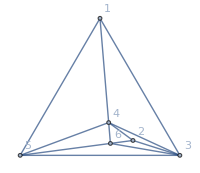
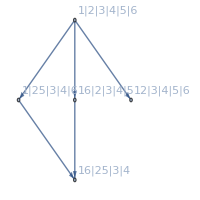
-Graphics-→-Graphics-

```mathematica
Graph[EdgeList[allGraphs6[2330248,"graph"]],GraphLayout->"TutteEmbedding",ImageSize->200, VertexLabels->"Name"]->FormulaGraph2[allGraphs6[2330248,"colofour"]]
```

```mathematica
maxminbis=Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},ChromaticPolynomial[g,4]==24&&ChromaticPolynomial[g,3]==0&& PlanarGraphQ[g]]&]
```

{7174458,7174466,7174446,7174442,7174471,7174489,7174435,7174416,7174414,7174531,7174537,7174562,7174506,7174368,7174375,7174360,7174398,7174346,7174342,7174336,7174695,7174697,7174726,7174666,7174786,7174606,7174206,7174211,7174200,7174234,7174182,7174186,7174174,7174282,7174128,7174126,7174138,7175173,7175191,7175263,7175101,7175425,7174939,7173733,7173714,7173712,7173805,7173642,7173616,7173967,7173478,7173454,7176637,7176643,7176667,7176613,7176883,7176397,7177370,7175910,7172262,7172269,7172254,7172293,7172238,7172158,7172509,7172014,7171942,7172994,7171538,7171534,7171528,7171510,7171456,7181013,7181015,7181041,7180987,7181095,7180933,7181746,7180282,7183210,7178818,7167888,7167893,7167882,7167919,7167862,7167973,7167802,7167622,7167568,7168618,7167162,7167166,7167154,7167136,7166920,7170070,7165704,7165702,7165714,7165624,7165462,7194135,7194137,7194139,7194133,7194145,7194127,7194892,7193380,7196404,7191868,7200940,7187332,7154771,7154773,7154779,7154742,7154740,7154688,7154680,7154524,7154518,7155472,7154040,7154038,7154068,7153960,7153798,7156876,7152582,7152574,7152556,7152664,7152340,7161088,7148206,7148200,7148182,7148128,7148452,7233493,7233511,7233583,7233421,7233745,7233259,7235689,7231315,7240063,7226941,7253185,7213819,7115413,7115394,7115392,7115485,7115322,7115296,7115647,7115158,7115134,7117591,7113216,7112488,7121965,7108840,7108114,7135087,7095694,7094992,7351597,7351603,7351627,7351573,7351843,7351357,7352329,7350871,7358161,7345039,7371283,7331917,7410650,7292550,6997302,6997309,6997294,6997333,6997278,6997198,6997549,6997054,6996982,6998035,6996576,6994390,7003867,6990736,6988558,7016989,6977542,6975436,7056354,6938258,6938254,6938248,6938230,6938176,6937528,6936070,7705893,7705895,7705921,7705867,7705975,7705813,7706623,7705165,7708081,7703707,7725577,7686211,7764946,7646842,7883050,7528738,6643008,6643013,6643002,6643039,6642982,6643093,6642922,6642742,6642688,6643741,6642280,6645199,6640816,6635722,6634264,6662695,6623086,6616768,6702058,6583962,6583966,6583954,6583936,6583720,6583234,6577402,6820150,6465864,6465862,6465874,6465784,6465622,6463678,6459304,8768775,8768777,8768779,8768773,8768785,8768767,8769505,8768047,8770963,8766589,8775337,8762215,8827852,8709700,8946004,8591548,9300460,8237092,5580131,5580133,5580139,5580102,5580100,5580048,5580040,5579884,5579878,5580859,5579374,5582317,5577862,5586691,5573326,5559718,5558260,5553886,5639152,5521080,5521078,5521108,5521000,5520838,5520352,5501398,5757196,5402982,5402974,5402956,5403064,5402740,5400796,5383300,6111328,5048686,5048680,5048662,5048608,5048932,5042128,5029006,11957421,11957423,11957425,11957419,11957431,11957413,11957449,11957395,11957503,11957341,11957665,11957179,12017200,11897644,12136756,11778088,12495424,11419420,13571428,10343416,2391485,2391487,2391493,2391511,2391565,2391727,2390754,2390752,2390728,2389296,2389288,2389216,2384920,2384914,2384680,2371774,2371720,2371558,2449804,2332434,2332432,2332408,2333164,2330248,2325874,2312752,2566444,2214336,2214328,2214256,2213608,2216524,2207776,2194654,2916364,1860040,1860034,1859800,1859314,1857856,1866604,1840360,3966124,797134,797080,796918,796432,794974,790600,816844}

```mathematica
Synop[k_]:=Labeled[Graph[EdgeList[allGraphs6[k,"graph"]],GraphLayout->"PlanarEmbedding",ImageSize->200, VertexLabels->"Name"],k]->FormulaGraph2[allGraphs6[k,"colofour"]]
```

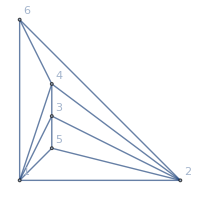
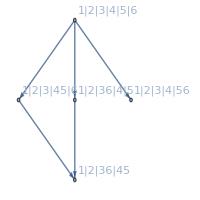
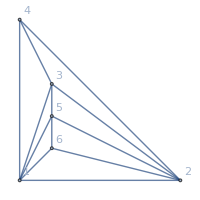
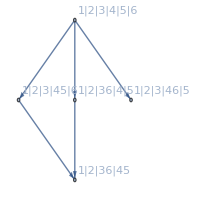
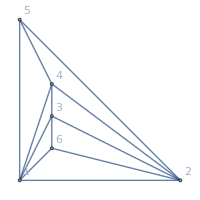
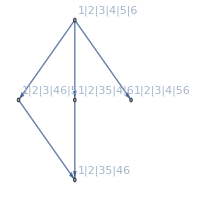
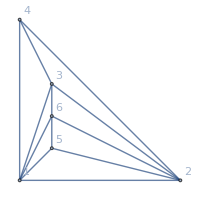
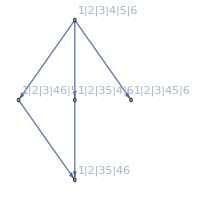
{-Graphics-7174416→-Graphics-,-Graphics-7174414→-Graphics-,-Graphics-7174368→-Graphics-,-Graphics-7174360→-Graphics-,-Graphics-7174342→-Graphics-,-Graphics-7174336→-Graphics-,-Graphics-7174206→-Graphics-,-Graphics-7174200→-Graphics-,-Graphics-7174182→-Graphics-,-Graphics-7174174→-Graphics-,-Graphics-7174128→-Graphics-,-Graphics-7174126→-Graphics-,-Graphics-7173714→-Graphics-,-Graphics-7173712→-Graphics-,-Graphics-7173642→-Graphics-,-Graphics-7173616→-Graphics-,-Graphics-7173478→-Graphics-,-Graphics-7173454→-Graphics-,-Graphics-7172262→-Graphics-,-Graphics-7172254→-Graphics-,-Graphics-7172238→-Graphics-,-Graphics-7172158→-Graphics-,-Graphics-7172014→-Graphics-,-Graphics-7171942→-Graphics-,-Graphics-7171534→-Graphics-,-Graphics-7171528→-Graphics-,-Graphics-7171510→-Graphics-,-Graphics-7171456→-Graphics-,-Graphics-7167888→-Graphics-,-Graphics-7167882→-Graphics-,-Graphics-7167862→-Graphics-,-Graphics-7167802→-Graphics-,-Graphics-7167622→-Graphics-,-Graphics-7167568→-Graphics-,-Graphics-7167162→-Graphics-,-Graphics-7167154→-Graphics-,-Graphics-7167136→-Graphics-,-Graphics-7166920→-Graphics-,-Graphics-7165704→-Graphics-,-Graphics-7165702→-Graphics-,-Graphics-7165624→-Graphics-,-Graphics-7165462→-Graphics-,-Graphics-7154742→-Graphics-,-Graphics-7154740→-Graphics-,-Graphics-7154688→-Graphics-,-Graphics-7154680→-Graphics-,-Graphics-7154524→-Graphics-,-Graphics-7154518→-Graphics-,-Graphics-7154040→-Graphics-,-Graphics-7154038→-Graphics-,-Graphics-7153960→-Graphics-,-Graphics-7153798→-Graphics-,-Graphics-7152582→-Graphics-,-Graphics-7152574→-Graphics-,-Graphics-7152556→-Graphics-,-Graphics-7152340→-Graphics-,-Graphics-7148206→-Graphics-,-Graphics-7148200→-Graphics-,-Graphics-7148182→-Graphics-,-Graphics-7148128→-Graphics-,-Graphics-7115394→-Graphics-,-Graphics-7115392→-Graphics-,-Graphics-7115322→-Graphics-,-Graphics-7115296→-Graphics-,-Graphics-7115158→-Graphics-,-Graphics-7115134→-Graphics-,-Graphics-7113216→-Graphics-,-Graphics-7112488→-Graphics-,-Graphics-7108840→-Graphics-,-Graphics-7108114→-Graphics-,-Graphics-7095694→-Graphics-,-Graphics-7094992→-Graphics-,-Graphics-6997302→-Graphics-,-Graphics-6997294→-Graphics-,-Graphics-6997278→-Graphics-,-Graphics-6997198→-Graphics-,-Graphics-6997054→-Graphics-,-Graphics-6996982→-Graphics-,-Graphics-6996576→-Graphics-,-Graphics-6994390→-Graphics-,-Graphics-6990736→-Graphics-,-Graphics-6988558→-Graphics-,-Graphics-6977542→-Graphics-,-Graphics-6975436→-Graphics-,-Graphics-6938254→-Graphics-,-Graphics-6938248→-Graphics-,-Graphics-6938230→-Graphics-,-Graphics-6938176→-Graphics-,-Graphics-6937528→-Graphics-,-Graphics-6936070→-Graphics-,-Graphics-6643008→-Graphics-,-Graphics-6643002→-Graphics-,-Graphics-6642982→-Graphics-,-Graphics-6642922→-Graphics-,-Graphics-6642742→-Graphics-,-Graphics-6642688→-Graphics-,-Graphics-6642280→-Graphics-,-Graphics-6640816→-Graphics-,-Graphics-6635722→-Graphics-,-Graphics-6634264→-Graphics-}

```mathematica
Table[Synop[k],{k,Take[Select[maxminbis,VertexCount[allGraphs6[#,"graph"]]==6&],100]}]
```

## Now for some plantri graphs

```mathematica
FindFullFormula[g_,v_]:=Block[{edge,pos1,pos2,v2},
If[CompleteGraphQ[g],
{SetsToSymbol2[v]},
edge=First[EdgeList[GraphComplement[g]]];
Table[If[MemberQ[v[[k]],edge[[1]]],pos1=k],{k,Length[v]}];
Table[If[MemberQ[v[[k]],edge[[2]]],pos2=k],{k,Length[v]}];
v2=v;
v2[[pos1]]=Join[v2[[pos1]],v2[[pos2]]];
v2=Delete[v2,pos2];
Join[
FindFullFormula[EdgeAdd[g,edge],v],
FindFullFormula[VertexContract[g,{edge[[1]],edge[[2]]}],v2]
]
]
]
```

```mathematica
Monitor[Table[k->ChromaticPolynomial[Graph[plantri[[k]]],4],{k,1,100}],k]
```

{1→240,2→480,3→768,4→720,5→648,6→1008,7→384,8→528,9→768,10→960,11→1056,12→720,13→1152,14→912,15→1248,16→1272,17→816,18→1536,19→1872,20→1272,21→1152,22→1248,23→2016,24→1536,25→1152,26→1248,27→1920,28→1728,29→1560,30→1200,31→1968,32→1248,33→864,34→1200,35→1656,36→2136,37→1440,38→1560,39→1440,40→1800,41→2496,42→2160,43→1920,44→1632,45→1536,46→1656,47→2304,48→2064,49→2064,50→2208,51→2328,52→1488,53→3072,54→2256,55→2088,56→1728,57→2304,58→2400,59→2544,60→1488,61→1704,62→3648,63→1728,64→2016,65→1968,66→1536,67→2448,68→1920,69→1488,70→2112,71→1728,72→3048,73→1968,74→2352,75→1296,76→1608,77→2136,78→1848,79→1776,80→1848,81→1632,82→1608,83→1728,84→1896,85→1632,86→1608,87→1824,88→3552,89→1728,90→1824,91→1368,92→2208,93→2352,94→1584,95→1728,96→2592,97→1728,98→2088,99→2304,100→2592}

```mathematica
Select[Take[plantri,10],ChromaticPolynomial[Graph[#],4]==24&]
```

$Aborted

```mathematica
gg=Graph[plantri[[1]]]
```

-Graphics-

```mathematica
VertexCount[gg]
```

12

```mathematica
FindFullFormula[gg,Table[{k},{k,12}]]
```

{n1x2x3x4x5x6x7x8x9x10x11x12,n1x2x3x4x5x6x7x8x911x10x12,n1x2x3x4x5x6x7x811x9x10x12,n1x2x3x4x5x6x7x810x9x11x12,n1x2x3x4x5x6x7x810x911x12,n1x2x3x4x5x6x710x8x9x11x12,n1x2x3x4x5x6x710x8x911x12,n1x2x3x4x5x6x710x811x9x12,n1x2x3x4x5x6x79x8x10x11x12,n1x2x3x4x5x6x79x811x10x12,n1x2x3x4x5x6x79x810x11x12,n1x2x3x4x5x612x7x8x9x10x11,n1x2x3x4x5x612x7x8x911x10,n1x2x3x4x5x612x7x811x9x10,n1x2x3x4x5x612x7x810x9x11,26763,n179x2411x3512x68x10,n179x24x35x6810x11x12,n179x24x3512x6810x11,n179x2412x35x6810x11,n179x2411x35x6810x12,n179x2411x3512x6810,n17x24x35x68x911x10x12,n17x24x3512x68x911x10,n17x2412x35x68x911x10,n17x24x35x6810x911x12,n17x24x3512x6810x911,n17x2412x35x6810x911,n1710x24x35x68x911x12,n1710x24x3512x68x911,n1710x2412x35x68x911}
 |  |  |  |

```mathematica
JacobsThalGraph[3]
```

-Graphics-

```mathematica
FormulaGraph2[Fold[Plus,FindFullFormula[JacobsThalGraph[3],Table[{k},{k,8}]]]]
```

-Graphics-

```mathematica
With[{g=JacobsThalGraph[3]},FormulaGraph2[Fold[Plus,FindFullFormula[g,Table[{i},{i,VertexCount[g]}]]]]]
```

-Graphics-

```mathematica
Table[With[{g=JacobsThalGraph[k]},FormulaGraph2[Fold[Plus,FindFullFormula[g,Table[{i},{i,VertexCount[g]}]]]]],{k,1,7}]
```

{-Graphics-,-Graphics-,4,-Graphics-}
 |  |  |  |

```mathematica
Table[With[{g=JacobsThalGraph[k]},Length[FindFullFormula[g,Table[{i},{i,VertexCount[g]}]]]],{k,1,6}]
```

{2,8,22,82,324,1430}

```mathematica
Table[ChromaticPolynomial[JacobsThalGraph[k],3],{k,1,10}]
```

{0,6,0,6,0,6,0,6,0,6}

```mathematica
Table[MaximalPlanarQ[JacobsThalGraph[k]],{k,1,10}]
```

{True,True,True,True,True,True,True,True,True,True}